# Non-Hermitian Fermi-Dirac Distribution in Persistent Current Transport

Authors: Pei-Xin Shen, Zhide Lu, Jose Lado, and Mircea Trif
Reference: Non-Hermitian Persistent Current Transport, arXiv:2403.09569.
License: MIT

# Non-Hermitian Fermi-Dirac Distribution in Eq. (8)

## Derivation

Integrand Poles

```mathematica
Clear["Global`*"];
(*the integrand in Eq.(S14)*)
integrand=1/(Exp[β ω]+1)1/(ω-ε);
FullSimplify@FunctionPoles[integrand,ω]
```

{{ε,1},{ConditionalExpression[(ⅈ (π+2 π C[1]))/β, C[1]∈ℤ],1}}

Useful Identities

```mathematica
(*Idenities used in Eq.(S15)*)
FullSimplify[{
Sum[1/(m+z-1),{m,M}]==PolyGamma[M+z]-PolyGamma[z],
PolyGamma[1-z]-PolyGamma[z]==π Cot[π z],
PolyGamma[1/2+ⅈ (β ε)/(2 π)]+PolyGamma[1/2-ⅈ (β ε)/(2 π)]==PolyGamma[1/2+ⅈ (β ε)/(2 π)]+PolyGamma[1-(1/2+ⅈ (β ε)/(2 π))]==2PolyGamma[1/2+ⅈ (β ε)/(2 π)]+π Cot[π (1/2+ⅈ (β ε)/(2 π))],
π Cot[π (1/2+ⅈ (β ε)/(2 π))]==ⅈ π (1/(1+ⅇ^(+β ε))-1/(1+ⅇ^(-β ε)))}]
```

{True,True,True,True}

```mathematica
(*Idenities used in Eq.(S23)*)
FullSimplify[LogGamma[z]+LogGamma[1-z]==Log[π]-Log@Sin[π z]==Log[π Csc[π z]],Assumptions->{0<z<1}]
```

True

Lower Half

```mathematica
Block[{β=1,R=10,ε=1-ⅈ},
Show[ComplexPlot[integrand,{ω,-R-R ⅈ,+R+R ⅈ},ColorFunction->"MaxAbs"],RegionPlot@Disk[{0,0},R,{π,2π}],ImageSize->Medium]]
```

-Graphics-

```mathematica
(*the residue of the complex eigenvalue in the lower half of the complex plane*)
FullSimplify[-2π ⅈ Residue[integrand,{ω,ε}]]
```

-(2 ⅈ π)/(1+ⅇ^(β ε))

```mathematica
(*the residue of the singlarity along the negative imaginary axis*)
FullSimplify@Block[{M=6},
Sum[-2π ⅈ Residue[integrand,{ω,(m-1/2)2π ⅈ/β}],{m,-M+1,0}]==-Sum[(+m-1/2-(ⅈ β ε)/(2π))^-1,{m,1,M}]==-(PolyGamma[+M+1/2-(ⅈ β ε)/(2π)]-PolyGamma[+1/2-(ⅈ β ε)/(2π)])]
```

True

Upper Half

```mathematica
Block[{β=1,R=10,ε=1-ⅈ},
Show[ComplexPlot[integrand,{ω,-R-R ⅈ,+R+R ⅈ},ColorFunction->"MaxAbs"],RegionPlot@Disk[{0,0},R,{0,π}],ImageSize->Medium]]
```

-Graphics-

```mathematica
(*the residue of the singlarity along the positive imaginary axis*)
FullSimplify@Block[{M=6},
Sum[+2π ⅈ Residue[integrand,{ω,(m-1/2)2π ⅈ/β}],{m,1,+M,1}]==-Sum[(+m-1/2+(ⅈ β ε)/(2π))^-1,{m,1,M}]==-(PolyGamma[+M+1/2+(ⅈ β ε)/(2π)]-PolyGamma[+1/2+(ⅈ β ε)/(2π)])]
```

True

Average Two Contours

```mathematica
(*Obtain the non-Hermitian Fermi-Dirac Distribution in Eq.(8)*)
FullSimplify[1/2(-(2 ⅈ π)/(1+ⅇ^(β ε))+PolyGamma[+1/2+(ⅈ β ε)/(2π)]+PolyGamma[+1/2-(ⅈ β ε)/(2π)])==PolyGamma[+1/2+(ⅈ β ε)/(2π)]-(ⅈ π)/2]
```

True

## Visualization

```mathematica
Clear["Global`*"];
feff[ε_]:=-1/π Log[ε];
FunctionAnalytic[{feff[ε],Im[ε]<0},ε,Complexes]
```

True

```mathematica
Block[{ε=r Exp[ⅈ ϕ]},
axesArrows=Graphics3D[{Arrowheads[0.05],
Arrow[{{0,0,0},{1.2,0,0}}],Text["Re ε",{1.1,-0.2,0}],
Arrow[{{0,0,0},{0,-0.9,0}}],Text["Im ε",{-0.2,-0.8,0}],
Arrow[{{0,0,0},{0,0,1.2}}],Text["Θ(-ϵ)",{0.3,0,0.6}],
Text["-1/πIm[ln(ε)]",{0,0,1.3}],Text["Im[(ε)]",{-0.5,0,0.5}]},
Boxed->False,ViewPoint->{5,-10,5},AspectRatio->2/3,BaseStyle->{FontFamily->"Times",FontSize->24}];
feffZero=Show[axesArrows,
ParametricPlot3D[{Re@ε,Im@ε,Im@feff[ε]},{r,0,1},{ϕ,π,2π},PlotStyle->Opacity[0.5],Mesh->None,ColorFunction->(Hue[#5]&),Axes->False],ParametricPlot3D[{ϵ,0,fFD[ϵ]},{ϵ,-1,1},PlotStyle->{Black,Dashing[0.012],Thickness[0.01]},ExclusionsStyle->{{Black,Dashing[0.015],Thickness[0.01]},Black}],ParametricPlot3D[{x,0,z},{x,-1,1},{z,0,1},Mesh->None,PlotStyle->Directive[Gray,Opacity[0.1]]],ImageSize->350,Method->{"ShrinkWrap"->True}]]
```

-Graphics3D-

```mathematica
Clear["Global`*"];
feff[ε_,β_]:=-1/π(PolyGamma[1/2+(ⅈ β ε)/(2 π)]-(ⅈ π)/2);
FunctionAnalytic[{feff[ε,β],Im[ε]<0},ε,Complexes,Assumptions->β>0]
```

True

```mathematica
Block[{β=20,ε=r Exp[ⅈ ϕ]},
axesArrows=Graphics3D[{Arrowheads[0.05],
Arrow[{{0,0,0},{1.2,0,0}}],Text["Re ε",{1.1,-0.2,0}],
Arrow[{{0,0,0},{0,-0.9,0}}],Text["Im ε",{-0.2,-0.8,0}],
Arrow[{{0,0,0},{0,0,1.2}}],Text["",{0.4,0,0.6}],
Text["-1/π",{0.1,0,1.5}],Text["Im[(ε, β)]",{-0.5,0,0.5}]},
Boxed->False,ViewPoint->{5,-10,5},AspectRatio->2/3,BaseStyle->{FontFamily->"Times",FontSize->24}];
feffFinite=Show[axesArrows,ParametricPlot3D[{Re@ε,Im@ε,-1/π Im[(PolyGamma[1/2+ⅈ (β ε)/(2 π)]-(ⅈ π)/2)]},{r,0,1},{ϕ,π,2π},PlotStyle->Opacity[0.5],Mesh->None,ColorFunction->(Hue[#5]&),Axes->False],ParametricPlot3D[{ϵ,0,1/(1+Exp[β ϵ])},{ϵ,-1,1},PlotStyle->{Black,Dashing[0.012],Thickness[0.01]}],ParametricPlot3D[{x,0,z},{x,-1,1},{z,0,1},Mesh->None,PlotStyle->Directive[Gray,Opacity[0.1]]],ImageSize->350,Method->{"ShrinkWrap"->True}]]
```

-Graphics3D-

## Asymptotic Behavior

Distribution and Free Energy

```mathematica
Clear["Global`*"];
(*non-Hermitian Fermi-Dirac distribution *)
feff[ε_]:=-1/π Log[ε];
(*non-Hermitian Fermi-Dirac distribution *)
feff[ε_,β_]:=-1/π(PolyGamma[1/2+(ⅈ β ε)/(2 π)]-(ⅈ π)/2);
(*log-gamma function in the non-Hermitian free energy  of Eq.(9)*)
ℱeff[ε_,β_]:=1/β(ℱLogGamma[ε,β]+ℱLogGamma[-ε*,β]);ℱLogGamma[ε_,β_]:=LogGamma[1/2+(ⅈ β ε)/(2 π)];
(*symbolic conjugate*)
𝒦[operator_]:=operator/.Complex[x_,y_]:>Complex[x,-y];
```

Hermitian Limit ()

```mathematica
(* in Eq.(S21)*)
Limit[feff[ϵ-ⅈ η],η->0,Assumptions->#,Direction->"FromAbove"]&/@{ϵ<0,ϵ>0}
```

{ⅈ-Log[-ϵ]/π,-Log[ϵ]/π}

```mathematica
(* in Eq.(S21), here we already assume ϵ is real and use symbolic conjugate 𝒦 to do the conjugate*)
FullSimplify[feff[ϵ,β]==1/2(feff[ϵ,β]+𝒦@feff[ϵ,β])+1/2(feff[ϵ,β]-𝒦@feff[ϵ,β])==1/2(feff[ϵ,β]+𝒦@feff[ϵ,β])+ⅈ 1/(ⅇ^(β ϵ)+1)]
```

True

```mathematica
(*Idenities used in  below Eq.(S22)*)
SeedRandom[0608];
Block[{β=RandomReal@{5,10},ϵ=RandomReal@{-10,10},η=10^-8,ε},ε=ϵ-ⅈ η;Chop[{
ℱeff[ε,β],2/β Re@ℱLogGamma[ε,β],1/β(ℱLogGamma[ε,β]+ℱLogGamma[-ε*,β]),
1/β(Log[2π]+(β ε)/2-Log[1+ ⅇ^(β ε)]),1/β(Log[2π]-Log[ ⅇ^(+(β ε)/2)+ ⅇ^(-(β ε)/2)])},10^-6]]
```

{-0.923937,-0.923937,-0.923937,-0.923937,-0.923937}

Zero Temperature ()

```mathematica
(*Idenity used in Eq.(S22)*)
FullSimplify@PowerExpand[Asymptotic[feff[ε,β],{β,∞,2},Assumptions->{β>0,ε>0}]==-1/π(Log[β/(2 π)]+Log[ε]-π^2/(6 β^2 ε^2))]
```

True

```mathematica
(*Idenity used below Eq.(S23)*)
FullSimplify@PowerExpand[Asymptotic[1/β ℱLogGamma[ε,β],{β,∞,3}]==ⅈ/(2 π)(ε Log[ε]+ε Log[(ⅈ β)/(2 π ⅇ)])+Log[2 π]/(2 β)+(ⅈ π)/(12 β^2 ε)]
```

True

Infinite Temperature ()

```mathematica
(*Idenity used in Eq.(S22)*)
FullSimplify[Normal@Series[feff[ε,β],{β,0,1},Assumptions->{β>0,ε>0}]==-1/π(PolyGamma[1/2] -ⅈ π (1/2-(β ε)/4))]
```

True

```mathematica
(*Idenity used below Eq.(S23)*)
FullSimplify[Normal@Series[1/β ℱLogGamma[ε,β],{β,0,1}]==Log[π]/(2 β)+(ⅈ PolyGamma[1/2])/(2 π)ε -(β ε^2)/16]
```

True

# Current Continuity at Exceptional Points

## Toy Model

Biorthogonal Eigensystems

```mathematica
Clear["Global`*"];
ℋeff=({{0, 1}, {1, -2ⅈ κ}});
{symbolicValsR,symbolicVecsR}=FullSimplify[Reverse[Eigensystem[ℋeff]ᵀ]ᵀ];
{εp,εm}=symbolicValsR
(*-1/(√2)symbolicVecsR==1/(√2)({{εm, εp}, {-1, -1}})ᵀ//Simplify*)
symbolicVecsR=1/(√2)({{εm, εp}, {-1, -1}})ᵀ;
symbolicVecsL=FullSimplify[Inverse[symbolicVecsR]†];
(*symbolicVecsL==((√2)/(εp-εm)({{-1, -εp}, {+1, +εm}}))*//FullSimplify*)
symbolicVecsL=((√2)/(εp-εm)({{-1, -εp}, {+1, +εm}}))*;
ℋeff==symbolicVecsRᵀ.DiagonalMatrix[symbolicValsR].symbolicVecsL*//FullSimplify
```

{-ⅈ κ+√(1-κ^2),-ⅈ κ-√(1-κ^2)}

True

Observables computed via Eq. (5) and Eq. (8)

```mathematica
feff[ε_]:=-1/π Log[ε];feff[ε_,β_]:=-1/π(PolyGamma[1/2+(ⅈ β ε)/(2 π)]-(ⅈ π)/2);
(*arbitray parameters*)
Block[{κ=0.9,β=1,O,O11=0.3,O22=-0.2,O21,O12=0.8-0.8ⅈ},O21=O12*;O={{O11,O12},{O21,O22}};
{{Im@Tr[O.MatrixFunction[feff,ℋeff]],2Re[O12]Im[(feff@εp-feff@εm)/(εp-εm)]+(O11+O22)/2},{Im@Tr[O.MatrixFunction[feff[#,β]&,ℋeff]],2 Re[O12]Im[(feff[εp,β]-feff[εm,β])/(εp-εm)]+(O11+O22)/2}}]
```

{{-0.476982,-0.476982},{-0.210784,-0.210784}}

```mathematica
(*symbolic limit at the exceptional point*)
εEP=εp/.κ->1;
Block[{O,O11,O22,O21,O12},O21=O12*;O={{O11,O12},{O21,O22}};FullSimplify[Im@Limit[
{Tr[O.MatrixFunction[feff,ℋeff]],
Tr[O.MatrixFunction[feff[#,β]&,ℋeff]]},κ->1],{O11>0,O22>0,,β>0}]]
```

{1/2 (O11+O22-(4 Re[O12])/π),1/2 (O11+O22-(2 β PolyGamma[1,(π+β)/(2 π)] Re[O12])/π^2)}

```mathematica
(*numerical value at the exceptional point*)
Block[{κ=1,β=1,O,O11=0.3,O22=-0.2,O21,O12=0.8-0.8ⅈ},O21=O12*;O={{O11,O12},{O21,O22}};
{{Im@Tr[O.MatrixFunction[feff,ℋeff]],2Re[O12]Im[D[feff[ε],ε]/.{ε->εEP}]+(O11+O22)Im@feff[εEP],Re[O12](-2/π)+(O11+O22)/2},
{Im@Tr[O.MatrixFunction[feff[#,β]&,ℋeff]],2 Re[O12]Im[D[feff[ε,β],ε]/.{ε->εEP}]+(O11+O22)Im@feff[εEP,β],Re[O12](-β/π^2 PolyGamma[1,1/2+β/(2 π)])+(O11+O22)/2}}]
```

{{-0.459296,-0.459296,-0.459296},{-0.202918,-0.202918,-0.202918}}

## Section II D in Supplemental Material

Distribution and Free Energy

```mathematica
Clear["Global`*"];
(*non-Hermitian Fermi-Dirac distribution *)
feff[ε_]:=-1/π Log[ε];
(*non-Hermitian Fermi-Dirac distribution *)
feff[ε_,β_]:=-1/π(PolyGamma[1/2+(ⅈ β ε)/(2 π)]-(ⅈ π)/2);
(*log-gamma function in the non-Hermitian free energy  of Eq.(9)*)
ℱeff[ε_,β_]:=1/β(ℱLogGamma[ε,β]+ℱLogGamma[-ε*,β]);ℱLogGamma[ε_,β_:β]:=LogGamma[1/2+(ⅈ β ε)/(2 π)];
(*Eq.(S24)*)
εp[ϕ_]:=μ-ⅈ ν[ϕ]+√(+s[ϕ]);εm[ϕ_]:=μ-ⅈ ν[ϕ]-√(+s[ϕ]);
εp[ϕEP]=εm[ϕEP]=εEP=μ-ⅈ ν[ϕEP];
{D[εp[ϕ],ϕ],D[εm[ϕ],ϕ]}
```

{s'[ϕ]/(2 √s[ϕ])-ⅈ ν'[ϕ],-s'[ϕ]/(2 √s[ϕ])-ⅈ ν'[ϕ]}

Zero Temperature

```mathematica
FullSimplify[{
(*Eq.(S26)*)
D[εp[ϕ]Log@εp[ϕ]+εm[ϕ]Log@εm[ϕ],ϕ]==s'[ϕ]((Log@εp[ϕ]-Log@εm[ϕ])/(2 √s[ϕ]))-ⅈ ν'[ϕ](2+Log@εp[ϕ]+Log@εm[ϕ]),
(*Eq.(S27)*)
(Limit[D[εp[ϕ]Log@εp[ϕ]+εm[ϕ]Log@εm[ϕ],ϕ],s[ϕ]->0]/.ϕ->ϕEP)==s'[ϕEP]Log'@εEP-ⅈ ν'[ϕEP](2+2Log[μ-ⅈ ν[ϕEP]])==-π(s'[ϕEP](D[feff[ε],ε]/.ε->εEP)-2 ⅈ ν'[ϕEP](feff[εEP]-1/π))}]
```

{True,True}

Finite Temperature

```mathematica
(*Eq.(S28)*)
FullSimplify[(Limit[D[ℱLogGamma@εp[ϕ]+ℱLogGamma@εm[ϕ],ϕ],s[ϕ]->0]/.ϕ->ϕEP)==β/(2ⅈ)(s'[ϕEP](D[feff[ε,β],ε]/.ε->εEP)-2ⅈ ν'[ϕEP](feff[εEP,β]-ⅈ/2))]
```

True

# Non-Hermitian Effective Hamiltonian

## Green’s Function of a Fermionic Reservoir

Analytics Expression

```mathematica
Clear["Global`*"];
(*Eq.(S4)*)
GanalyticsSqrt[l_,m_,ω_]:=
Block[{x=(g-ω)/(2 t)},Piecewise[{{((-x-√(x^2-1))^Abs[l-m]-(-x-√(x^2-1))^Abs[l+m])/(+2t √(x^2-1)), x<-1}, {((-x-Sign[t]ⅈ √(1-x^2))^Abs[l-m]-(-x-Sign[t]ⅈ √(1-x^2))^Abs[l+m])/(+2Abs[t] ⅈ √(1-x^2)), -1<=x<=+1}, {((-x+√(x^2-1))^Abs[l-m]-(-x+√(x^2-1))^Abs[l+m])/(-2t √(x^2-1)), x>1}}]];
GanalyticsExp[l_,m_,ω_]:=
Block[{x=(g-ω)/(2 t),k=ArcCos[-x]},Piecewise[{{(Exp[+ⅈ k Abs[l-m]]-Exp[+ⅈ k Abs[l+m]])/(-2ⅈ t Sin[k]), x<-1}, {(Exp[-Sign[t]ⅈ k Abs[l-m]]-Exp[-Sign[t]ⅈ k Abs[l+m]])/(+2ⅈ Abs[t] Sin[k]), -1<=x<=+1}, {(Exp[-ⅈ k Abs[l-m]]-Exp[-ⅈ k Abs[l+m]])/(+2ⅈ t Sin[k]), x>1}}]];
```

Numerical Verification

```mathematica
Nt=100;
Hx=Normal@SparseArray[{{i_,i_}->Ε[i],{i_,j_}/;i==j+1->Τ[j],{i_,j_}/;j==i+1->Τ[i]},Nt];
Do[Ε[i]=g,{i,Nt}];Do[Τ[i]=t,{i,Nt-1}];
Gnumerics[l_,m_,ω_]:=Inverse[ω IdentityMatrix[Nt]-Hx][[l,m]];
Hx[[;;10,;;10]]//MatrixForm
```

(g | t | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
t | g | t | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | t | g | t | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | t | g | t | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | t | g | t | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | t | g | t | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | t | g | t | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | t | g | t | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | t | g | t
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | t | g)

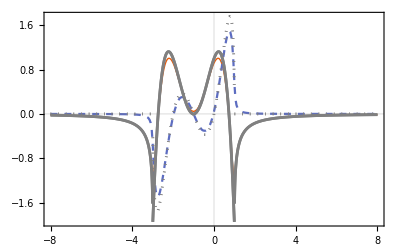

```mathematica
g=-1;t=-1;l=2;m=3;
ωMax=8;η=0.05;(*For calculating G[2,3,ω]*)
greenNumerics=ListPlot[ParallelMap[ReIm@Gnumerics[l,m,#+ⅈ η]&,Range[-ωMax,ωMax,η]]ᵀ,DataRange->{-ωMax,ωMax},PlotTheme->"Scientific",Joined->True,PlotRange->All,PlotStyle->{Thick,Dashed}];
greenAnalytics=ReImPlot[{GanalyticsSqrt[l,m,ω],GanalyticsExp[l,m,ω]},{ω,-ωMax,ωMax},PlotStyle->{Gray},PlotRange->All];
Show[greenNumerics,greenAnalytics,PlotRange->All]
```

## Edge Green’s Function for Self-Energy

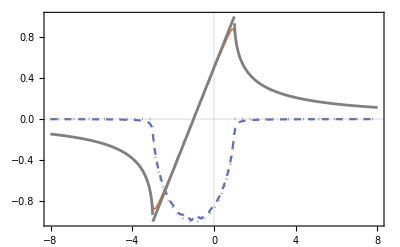

```mathematica
(*Eq.(S5) used for Eq.(S10)*)
GanalyticsSurface[ω_]:=1/(2 t^2)(ω-g+Piecewise[{{-Sign[t] √((ω-g)^2-(2t)^2), (g-ω)/(2 t)<-1}, {-ⅈ √((2t)^2-(ω-g)^2), -1<=(g-ω)/(2 t)<=+1}, {+Sign[t] √((ω-g)^2-(2t)^2), (g-ω)/(2 t)>1}}]);
g=-1;t=-1;l=1;m=1;
ωMax=8;η=0.05;
greenNumerics=ListPlot[ParallelMap[ReIm@Gnumerics[l,m,#+ⅈ η]&,Range[-ωMax,ωMax,η]]ᵀ,DataRange->{-ωMax,ωMax},PlotTheme->"Scientific",Joined->True,PlotRange->All,PlotStyle->{Thick,Dashed}];
greenAnalytics=ReImPlot[{(*GanalyticsSqrt[l,m,ω],GanalyticsExp[l,m,ω],*)GanalyticsSurface[ω]},{ω,-ωMax,ωMax},PlotStyle->{Gray},PlotRange->All];
Show[greenNumerics,greenAnalytics,PlotRange->All]
```